# Propagator-Polstellen für Residuensatz

In diesem Worksheet werden die Lösungen des Propagators A^{-2}  mithilfe von Fouriertransformationen für das Holo-Ndim-Modell bestimmt.
Ausführlich werden die Pole diskutiert, da Mathematica das Integral “für beliebige n” nicht einfach hinkriegt.

```mathematica
h[r_] = 1/(1+(l/r)^2);
hn[r_] = 1/(1+(l/r)^(2+n));
```

```mathematica
(* Fouriertransformierte von h *)
```

```mathematica
Assuming[p∈Reals ∧l>0,Integrate[ Exp[-I p r]* D[h[r],r],{r,-∞, ∞}]]
```

-ⅈ ⅇ^(-l Abs[p]) l p π

```mathematica
Solve[0≤ n<4&&n∈Integers,{n}]
```

{{n→0},{n→1},{n→2},{n→3}}

```mathematica
(* Fouriertransformierte von h in n dim *)
```

```mathematica
Assuming[p∈Reals ∧l>0∧n∈Integers ∧0≤ n≤ 7,Integrate[ Exp[-I p r]* D[hn[r],r],{r,-∞, ∞}]]
```

$Aborted

```mathematica
(* Fourier-Integral mit x=L*z  *) 
Assuming[p∈Reals ∧l>0∧n∈Integers ∧0≤ n≤ 7,Integrate[ Exp[-I p l z]* D[1/(1+(1/z)^(2+0)),z],{z,-∞, ∞}]]
```

-ⅈ ⅇ^(-l Abs[p]) l p π

```mathematica
Assuming[p∈Reals ∧l>0∧n∈Integers ∧0≤ n≤ 7,Integrate[ Exp[-I p l z]* D[1/(1+(1/z)^(2+4)),z],{z,-∞, ∞}]]
```

1/(6 Abs[p]^5)ⅇ^(-1/2 (2+ⅈ √3) l Abs[p]) ((-ⅈ+√3) ⅇ^(1/2 l Abs[p])-2 ⅈ ⅇ^(1/2 ⅈ √3 l Abs[p])-(ⅈ+√3) ⅇ^(1/2 (1+2 ⅈ √3) l Abs[p])) l p^6 π Sign[p]

```mathematica
(* Wie sieht eigentlich die Fouriertransformierte von der Lösung aus, die auf dem Paper steht? *)
ClearAll[p]
gFraktur[r_] = l/(Pi^2)    *(r^2 + l^2)^(-2);
Assuming[r∈Reals ∧p∈Reals ∧l>0 , 2Pi I /p * Integrate[ Exp[+I p r] * r * gFraktur[r],  {r,-∞,∞}]]
```

-ⅇ^(-l Abs[p])

```mathematica
D[gFraktur[r],r]
```

-(4 l r)/(π^2 (l^2+r^2)^3)

```mathematica
Integrate[Exp[-l p] Exp[I r p],{p,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^-l\ p + ⅈ\ p\ r does not converge on {-∞, ∞}.

∫_(-∞)^∞ ⅇ^(-l p+ⅈ p r)ⅆp

#### Untersuchung der Polstellen

```mathematica
(* Polstellengleichung *)
gleichung = Denominator[D[1/(1+(l/r)^(2+n)),r]] == 0
polstellen = Table[Solve[gleichung,r],{n,0,7}];
```

(1+(l^2 (l/r)^n)/r^2)^2 r^3==0

```mathematica
(* wie viele Polstellen gibt es pro n? *)
```

```mathematica
Grid[{
Prepend[Range[0,7],"n"],
Prepend[First /@ Dimensions  /@ polstellen,"# Polstellen"]
},
Frame -> All]
```

n | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
# Polstellen | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18

```mathematica
(* Eine Liste ueber n mit einer Liste der Polstellen-Werte ohne Ersetzungsregel r-> ... *)
polstellenWerte = polstellen /. {{r->b_}-> b} ;
```

```mathematica
(* wie lauten diese Polstellen? Eine Tabelle mit n links und den Polstellen rechts *)
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# Pole","Pole (unsortiert, mit allen Vielfachheiten)"}},
Table[{n,
First[Dimensions[polstellen[[n+1]]]],
Row[polstellenWerte[[n+1]] , ", "]},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # Pole | Pole (unsortiert, mit allen Vielfachheiten)
0 | 4 | , , -ⅈ l-ⅈ lⅈ lⅈ l
1 | 6 | , , -l-l1/2 (l-ⅈ √3 l)1/2 (l-ⅈ √3 l)1/2 (l+ⅈ √3 l)1/2 (l+ⅈ √3 l)
2 | 8 | , , -(-1)^(1/4) l-(-1)^(1/4) l(-1)^(1/4) l(-1)^(1/4) l-(-1)^(3/4) l-(-1)^(3/4) l(-1)^(3/4) l(-1)^(3/4) l
3 | 10 | , , -l-l1/4 (l+√5 l-ⅈ √(2 (5-√5)) l)1/4 (l+√5 l-ⅈ √(2 (5-√5)) l)1/4 (l+√5 l+ⅈ √(2 (5-√5)) l)1/4 (l+√5 l+ⅈ √(2 (5-√5)) l)1/4 (l-√5 l-√2 √(-5 l^2-√5 l^2))1/4 (l-√5 l-√2 √(-5 l^2-√5 l^2))1/4 (l-√5 l+√2 √(-5 l^2-√5 l^2))1/4 (l-√5 l+√2 √(-5 l^2-√5 l^2))
4 | 12 | , , -ⅈ l-ⅈ lⅈ lⅈ l-√(l^2/2-1/2 ⅈ √3 l^2)-√(l^2/2-1/2 ⅈ √3 l^2)√(l^2/2-1/2 ⅈ √3 l^2)√(l^2/2-1/2 ⅈ √3 l^2)-√(l^2/2+1/2 ⅈ √3 l^2)-√(l^2/2+1/2 ⅈ √3 l^2)√(l^2/2+1/2 ⅈ √3 l^2)√(l^2/2+1/2 ⅈ √3 l^2)
5 | 14 | , , -l-l(-1)^(1/7) l(-1)^(1/7) l-(-1)^(2/7) l-(-1)^(2/7) l(-1)^(3/7) l(-1)^(3/7) l-(-1)^(4/7) l-(-1)^(4/7) l(-1)^(5/7) l(-1)^(5/7) l-(-1)^(6/7) l-(-1)^(6/7) l
6 | 16 | , , -(-1)^(1/8) l-(-1)^(1/8) l(-1)^(1/8) l(-1)^(1/8) l-(-1)^(3/8) l-(-1)^(3/8) l(-1)^(3/8) l(-1)^(3/8) l-(-1)^(5/8) l-(-1)^(5/8) l(-1)^(5/8) l(-1)^(5/8) l-(-1)^(7/8) l-(-1)^(7/8) l(-1)^(7/8) l(-1)^(7/8) l
7 | 18 | , , -l-l(-1)^(1/9) l(-1)^(1/9) l-(-1)^(2/9) l-(-1)^(2/9) l(-1)^(1/3) l(-1)^(1/3) l-(-1)^(4/9) l-(-1)^(4/9) l(-1)^(5/9) l(-1)^(5/9) l-(-1)^(2/3) l-(-1)^(2/3) l(-1)^(7/9) l(-1)^(7/9) l-(-1)^(8/9) l-(-1)^(8/9) l

```mathematica
(* Wie lauten die Polstellen in POLARDARSTELLUNG? *)
(* Definition einer Umdarstellungsfunktion: *)
ComplexToPolar[z_]/;z∈Complexes:=Abs[z] Exp[I Arg[z]]
normPolstellenWerte = polstellenWerte /. {l-> 1};
```

```mathematica
(* Darstellung der Pole (Dopplungen entfernt, in Vielfachen von l)
  nach komplexen Winkeln sortiert *)
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n","Pole in Einheitswurzel-Darstellung","Winkel der Pole in komplexer Ebene"}},
Table[{
n,
Row[FullSimplify[ComplexToPolar /@ normPolstellenWerte[[n+1]]] // Union, ", "],
Row[FullSimplify[Arg /@ normPolstellenWerte[[n+1]]] // Union, ", "],
Row[Union[Arg /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a})], ", "]
},
{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | Pole in Einheitswurzel-Darstellung | Winkel der Pole in komplexer Ebene | 
0 | , , -ⅈⅈ | , , -π/2π/2 | , , 0π
1 | , , -1(-1)^(1/3)-(-1)^(2/3) | , , -π/3π/3π | , , 0-(2 π)/3(2 π)/3
2 | , , -(-1)^(1/4)(-1)^(1/4)-(-1)^(3/4)(-1)^(3/4) | , , -(3 π)/4-π/4π/4(3 π)/4 | , , 0-π/2π/2π
3 | , , -1(-1)^(1/5)-(-1)^(2/5)(-1)^(3/5)-(-1)^(4/5) | , , -(3 π)/5-π/5π/5(3 π)/5π | , , 0-(4 π)/5-(2 π)/5(2 π)/5(4 π)/5
4 | , , -ⅈⅈ-(-1)^(1/6)(-1)^(1/6)-(-1)^(5/6)(-1)^(5/6) | , , -(5 π)/6-π/2-π/6π/6π/2(5 π)/6 | , , 0-(2 π)/3-π/3π/3(2 π)/3π
5 | , , -1(-1)^(1/7)-(-1)^(2/7)(-1)^(3/7)-(-1)^(4/7)(-1)^(5/7)-(-1)^(6/7) | , , -(5 π)/7-(3 π)/7-π/7π/7(3 π)/7(5 π)/7π | , , 0-(6 π)/7-(4 π)/7-(2 π)/7(2 π)/7(4 π)/7(6 π)/7
6 | , , -(-1)^(1/8)(-1)^(1/8)-(-1)^(3/8)(-1)^(3/8)-(-1)^(5/8)(-1)^(5/8)-(-1)^(7/8)(-1)^(7/8) | , , -(7 π)/8-(5 π)/8-(3 π)/8-π/8π/8(3 π)/8(5 π)/8(7 π)/8 | , , 0-(3 π)/4-π/2-π/4π/4π/2(3 π)/4π
7 | , , -1(-1)^(1/9)-(-1)^(2/9)(-1)^(1/3)-(-1)^(4/9)(-1)^(5/9)-(-1)^(2/3)(-1)^(7/9)-(-1)^(8/9) | , , -(7 π)/9-(5 π)/9-π/3-π/9π/9π/3(5 π)/9(7 π)/9π | , , 0-(8 π)/9-(2 π)/3-(4 π)/9-(2 π)/9(2 π)/9(4 π)/9(2 π)/3(8 π)/9

```mathematica
(* Berechne die Vielfachheit der Pole. Sie ist offensichtlich
*IMMER* zwei!! *)
```

```mathematica
vielfachheit = Table[Count[normPolstellenWerte[[n+1]],# ] & /@ normPolstellenWerte[[n+1]], {n,0,7}]
```

```mathematica
{{2,2,2,2},{2,2,2,2,2,2},{2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}
```

{{2,2,2,2},{2,2,2,2,2,2},{2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}

```mathematica
ClearAll[MakePlot]
```

```mathematica
(* Zeichne die Polstellen *)
circle[s_Circle]:=s/.Circle[a_,r_,{start_,end_}]:>({s,Arrow[{#-r/10^2 {-Sin@end,Cos@end},#}]}&[a+r {Cos@end,Sin@end}])
MakePlot[n_,
label_:"Complex Cell[""]Cell[""]z plane of h_α(z) roots, compared to unit roots"
] :=Show[ListPlot[
{
{Re[#], Im[#]} & /@ normPolstellenWerte[[1+n]],
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a})
},
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},PlotStyle->{
Directive[Red,PointSize[.05],Opacity[0.7]],
Directive[Blue,PointSize[.05],Opacity[0.7]],
},
PlotRange-> All],
Graphics[{Opacity[0.2],Circle[{0,0},1]}],
Graphics@circle[Circle[{0,0},1,{0,Pi/(2+n)}]]
];
Manipulate[Show[MakePlot[n],
Graphics[Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{30,30},{0,0}]]]]
,{n,0,7,1}]
```

```mathematica
(* Veröffentlichungsreif machen... *)
```

```mathematica
Show[
GraphicsGrid[{
{MakePlot[2,"n=2"], MakePlot[3, "n=3"], MakePlot[7, "n=7"]}
}]
]
(* Manuell: "Complex Cell[""]Cell[""]z plane of h_α(z) roots, compared to unit roots" *)
```

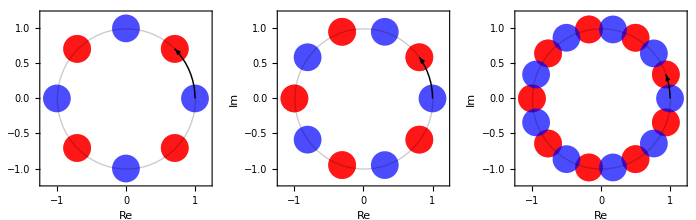
```mathematica
Export["wurzeln.pdf",-Graphics-]
```

wurzeln.pdf

```mathematica
(* Polstellenuntersuchung mit z=l*r statt r *)
```

```mathematica
D[1/(1+(1/z)^(2+n)),z]
```

((2+n) (1/z)^(3+n))/((1+(1/z)^(2+n))^2)

```mathematica
Solve[1/D[1/(1+(1/z)^(2+n)),z] == 0 , z]
```

{{z→(-1)^(1/(2+n))},{z→0^(1/(3+n))}}